```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0}]

## Diagrams generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[10]]&];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

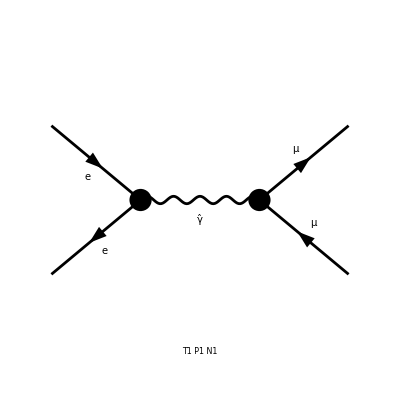

```mathematica
Paint[fieldsBorn];
```

```mathematica
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,Boxes,WFCorrections}];
topologies1L=topologies1L[[0]][topologies1L[[1]]];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[10]]&];
```

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

in total: 6 Particles amplitudes

Electron Mass to zero

```mathematica
ampBorn=ampBorn/.ME->0;
amp1L=amp1L/.ME->0;
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

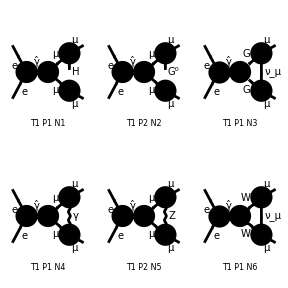

```mathematica
Paint[fields1L];
```

```mathematica
myAmpBorn=ExtractAmplitude[ampBorn];
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/feynArts_amplitudes/BornAmplitudes.m

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/feynArts_amplitudes/OneLoopAmplitudes.m

## Interference

```mathematica
ImportInput[]
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m.

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
smBorn=AmpSquare[myAmpBorn,myAmpBorn]//Simplify;
```

```mathematica
smBorn/.parameterReplace/.{I3l1->-1/2,Ql1->-1}
```

{(EL^4 Ql2^2 (4 mm^4+(-2+d) s^2-8 mm^2 t+4 s t+4 t^2))/s^2}

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn];
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon//interferences/Contribution_6_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,6},{j,1}]
```

ABISS: Integral family {{A0, {mh, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_1_1.m.

ABISS: Integral family {{A0, {mz, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_2_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_3_1.m.

ABISS: Integral family {{B0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_4_1.m.

ABISS: Integral family {{A0, {mz, mm}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_5_1.m.

ABISS: Integral family {{B0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/interferences/Contribution_6_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,6},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/kira_input/Contribution_6_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[B0,{m1},1,0,0,0]→0,userIntegral[A0,{m1,m2},1,0,1,0]→userIntegral[A0,{m1,m2},1,1,0,0],userIntegral[A0,{m1,m2},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[A0,{m1,m2},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[A0,{m1,m2},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+m1^2 (-s-2 t)+2 m2^2 t-s t+mm^2 (2 m1^2+2 m2^2+2 t)) userIntegral[A0,{m1,m2},1,1,1,0])/(4 mm^2-s),userIntegral[A0,{m1,m2},1,-1,1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},0,1,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-8+8 d) m1^2+(-56+24 d) m2^2+(12-4 d) s+(-16+16 d) t)+m2^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+m1^2 ((-4+2 d) s^2+(-8+8 d) s t+(-8+8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((16-8 d) s+(16-16 d) t)+m2^2 ((32-16 d) s+(48-16 d) t))) userIntegral[A0,{m1,m2},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+((mm^4+2 mm^2 t+t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((12-8 d) mm^8+(-2+d) m1^2 s t^2+(2-d) m2^2 s t^2+mm^6 ((-20+8 d) m1^2+(-12+8 d) m2^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((6-3 d) s+8 t)+m2^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 (-2 d s t+(12-8 d) t^2)+m2^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[A0,{m1,m2},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) m2^2+(8-8 d) t)+m2^4 (4 s t+(-4+4 d) t^2)+m1^4 ((-2+d) s^2+(-4+4 d) s t+(-4+4 d) t^2)+m1^2 (2 d s^2 t+(-4+4 d) s t^2)+mm^4 ((-4+4 d) m1^4+(-4+4 d) m2^4+(-4+4 d) s t+(-4+4 d) t^2+m2^2 ((-24+8 d) m1^2+16 t)+m1^2 ((-4+4 d) s+(-16+16 d) t))+m2^2 ((8-4 d) s t^2+m1^2 (-4 d s t+(8-8 d) t^2))+mm^2 ((-24+8 d) m2^4 t+(8-4 d) s t^2+m1^4 ((8-4 d) s+(8-8 d) t)+m1^2 (-8 d s t+(8-8 d) t^2)+m2^2 (-4 d s t+(-24+8 d) t^2+m1^2 ((8-4 d) s+16 t)))) userIntegral[A0,{m1,m2},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[A0,{m1,m2},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((mm^2+t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4-m1^2 t+m2^2 t+mm^2 (m1^2+m2^2+t)) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},1,1,-1,0]→(s userIntegral[A0,{m1,m2},0,1,0,0])/(2 mm^2)+((2 mm^2-s) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((m1^2 s-m2^2 s+mm^2 s) userIntegral[A0,{m1,m2},1,1,0,0])/(2 mm^2),userIntegral[A0,{m1,m2},0,0,1,0]→userIntegral[A0,{m1,m2},0,1,0,0],userIntegral[A0,{m1,m2},0,1,1,-1]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (2 m2^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[A0,{m1,m2},-1,1,1,0]→userIntegral[A0,{m1,m2},0,1,0,0]+1/2 (-2 m1^2+2 m2^2+2 mm^2-s) userIntegral[A0,{m1,m2},0,1,1,0],userIntegral[B0,{m1},1,0,1,0]→userIntegral[B0,{m1},1,1,0,0],userIntegral[B0,{m1},1,1,1,-1]→((2 mm^2-s-2 t) userIntegral[B0,{m1},0,1,1,0])/(4 mm^2-s)+((2 mm^2+2 t) userIntegral[B0,{m1},1,1,0,0])/(4 mm^2-s)+((-2 mm^4+2 m1^2 t-s t+mm^2 (2 m1^2+2 t)) userIntegral[B0,{m1},1,1,1,0])/(4 mm^2-s),userIntegral[B0,{m1},1,-1,1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,0,1,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,1,-2]→((3 mm^4+mm^2 (-s-2 t)-t^2) userIntegral[A0,{m1,m2},1,0,0,0])/(4 mm^4-mm^2 s)+(((8-8 d) mm^6+(2-d) s^3+4 s^2 t+(-4+4 d) s t^2+mm^4 ((-56+24 d) m1^2+(12-4 d) s+(-16+16 d) t)+m1^2 ((-4+2 d) s^2-8 s t+(8-8 d) t^2)+mm^2 ((-12+6 d) s^2-16 s t+(8-8 d) t^2+m1^2 ((32-16 d) s+(48-16 d) t))) userIntegral[B0,{m1},0,1,1,0])/((-64+32 d) mm^4+(32-16 d) mm^2 s+(-4+2 d) s^2)+(((12-8 d) mm^8+(2-d) m1^2 s t^2+mm^6 ((-12+8 d) m1^2+(-2+d) s+8 t)+mm^4 (-2 d s t+(-20+8 d) t^2+m1^2 ((2-d) s+(-40+16 d) t))+mm^2 ((6-3 d) s t^2+m1^2 ((8-2 d) s t+(-12+8 d) t^2))) userIntegral[B0,{m1},1,1,0,0])/((-32+16 d) mm^6+(16-8 d) mm^4 s+(-2+d) mm^2 s^2)+(((-4+4 d) mm^8+(8-4 d) m1^2 s t^2+(-2+d) s^2 t^2+mm^6 ((8-8 d) m1^2+(8-8 d) t)+m1^4 (4 s t+(-4+4 d) t^2)+mm^4 ((-4+4 d) m1^4+16 m1^2 t+(-4+4 d) s t+(-4+4 d) t^2)+mm^2 ((-24+8 d) m1^4 t+(8-4 d) s t^2+m1^2 (-4 d s t+(-24+8 d) t^2))) userIntegral[B0,{m1},1,1,1,0])/((-32+16 d) mm^4+(16-8 d) mm^2 s+(-2+d) s^2),userIntegral[B0,{m1},1,1,0,-1]→((mm^2-t) userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-mm^4+m1^2 t+mm^2 (m1^2+t)) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},1,1,-1,0]→(s userIntegral[A0,{m1,m2},1,0,0,0])/(2 mm^2)+((-m1^2 s+mm^2 s) userIntegral[B0,{m1},1,1,0,0])/(2 mm^2),userIntegral[B0,{m1},0,0,1,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},0,1,1,-1]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2-s) userIntegral[B0,{m1},0,1,1,0],userIntegral[B0,{m1},0,1,0,0]→userIntegral[A0,{m1,m2},1,0,0,0],userIntegral[B0,{m1},-1,1,1,0]→userIntegral[A0,{m1,m2},1,0,0,0]+1/2 (2 m1^2+2 mm^2-s) userIntegral[B0,{m1},0,1,1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,0,1,0],userIntegral[A0,{mh,mm},1,1,1,-1],userIntegral[A0,{mh,mm},1,-1,1,0],userIntegral[A0,{mh,mm},1,0,1,-1],userIntegral[A0,{mh,mm},1,1,1,-2],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mh,mm},1,1,0,-1],userIntegral[A0,{mh,mm},1,1,-1,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,0,1,0],userIntegral[A0,{mh,mm},0,1,1,-1],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},-1,1,1,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,0,1,0],userIntegral[A0,{mz,mm},1,1,1,-1],userIntegral[A0,{mz,mm},1,-1,1,0],userIntegral[A0,{mz,mm},1,0,1,-1],userIntegral[A0,{mz,mm},1,1,1,-2],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,0,-1],userIntegral[A0,{mz,mm},1,1,-1,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,0,1,0],userIntegral[A0,{mz,mm},0,1,1,-1],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},-1,1,1,0],userIntegral[B0,{mw},1,0,1,0],userIntegral[B0,{mw},1,1,1,-1],userIntegral[B0,{mw},1,1,1,0],userIntegral[B0,{mw},1,-1,1,0],userIntegral[B0,{mw},1,0,1,-1],userIntegral[B0,{mw},1,1,1,-2],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},1,0,0,0],userIntegral[B0,{mw},1,1,0,-1],userIntegral[B0,{mw},1,1,-1,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},0,0,1,0],userIntegral[B0,{mw},0,1,1,-1],userIntegral[B0,{mw},0,1,0,0],userIntegral[B0,{mw},-1,1,1,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,0,1,0],userIntegral[B0,{mm},1,1,1,-1],userIntegral[B0,{mm},1,-1,1,0],userIntegral[B0,{mm},1,0,1,-1],userIntegral[B0,{mm},1,1,1,-2],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},1,0,0,0],userIntegral[B0,{mm},1,1,0,-1],userIntegral[B0,{mm},1,1,-1,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[B0,{mm},0,0,1,0],userIntegral[B0,{mm},0,1,1,-1],userIntegral[B0,{mm},0,1,0,0],userIntegral[B0,{mm},-1,1,1,0]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Do[
SaveResult[i,j];
,{i,6},{j,1}]
```

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,6}]
```

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
```

```mathematica
minorReplace1={gAl->-Ql,gAu->-Qu,gAd->-Qd};
minorReplace2={gZlL->(I3l-Ql*sw^2)/(cw*sw),gZlR->(-Ql*sw^2)/(cw*sw),gZNL->(I3N)/(cw*sw),gZuL->(I3u-(Qu*sw^2))/(cw*sw),gZuR->(-Qu*sw^2)/(cw*sw),gZdL->(I3d-(Qd*sw^2))/(cw*sw),gZdR->(-Qd*sw^2)/(cw*sw)};
```

```mathematica
coefficients=Plus@@diagramCoefficients //Simplify
```

{(ⅈ EL^6 gHll^2 mm^2 (2 (-2+d) mm^2 (-4 mm^2+s)^2 (2 mm^4+2 (-2+d) s^2+mm^2 (s-10 t)+8 s t+8 t^2)+2 mh^4 (8 (-1+d) mm^6+4 mm^4 ((-1+d) s+4 (3-2 d) t)+s ((-2+d) s^2+4 s t+4 t^2)-4 mm^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2))-mh^2 (4 mm^2-s) (16 (-1+d) mm^6+4 mm^4 (d (s-18 t)+28 t)-(-4+d) s ((-2+d) s^2+4 s t+4 t^2)+4 mm^2 ((8-6 d+d^2) s^2+13 (-2+d) s t+2 (-12+7 d) t^2))) gAl[1]^2 gAl[2]^2)/(16 (-2+d) π^4 s^2 (-4 mm^2+s)^2),-((ⅈ EL^6 gHll^2 mm^2 (-2 (-2+d) mm^2 (4 mm^2-s) (8 mm^4+(-4+d) s^2+18 s t+20 t^2-2 mm^2 ((-9+2 d) s+18 t))+mh^2 (16 (-3+2 d) mm^6+4 mm^4 ((-12+7 d) s+8 (7-4 d) t)-2 mm^2 (9 (-2+d) s^2-48 (-2+d) s t+8 (11-6 d) t^2)+s (3 (-2+d) s^2+2 (14-5 d) s t+4 (8-3 d) t^2))) gAl[1]^2 gAl[2]^2)/(16 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),-((ⅈ EL^6 gHll^2 mm^2 (-2 mh^2 (8 (-1+d) mm^6+4 mm^4 ((-1+d) s+4 (3-2 d) t)+s ((-2+d) s^2+4 s t+4 t^2)-4 mm^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2))+(4 mm^2-s) (8 (-1+d) mm^6+4 mm^4 (s+2 (8-5 d) t)-(-3+d) s ((-2+d) s^2+4 s t+4 t^2)+4 mm^2 ((6-5 d+d^2) s^2+8 (-2+d) s t+2 (-7+4 d) t^2))) gAl[1]^2 gAl[2]^2)/(16 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),-(ⅈ EL^6 gHll^2 mm^2 (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2]^2)/(16 π^4 (4 mm^2-s) s^2),(ⅈ EL^6 gHll^2 mm^2 (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2]^2)/(16 π^4 (4 mm^2-s) s^2),(ⅈ EL^6 gAl[1]^2 gAl[2]^2 (2 gXll^2 mm^2 (64 (-2+d) mm^10-64 mm^8 ((-1+d) mz^2+(-2+d) t)+mz^2 s (2 mz^2-(-4+d) s) ((-2+d) s^2+4 s t+4 t^2)+4 mm^6 (4 (-1+d) mz^4-(-2+d) s (3 s-8 t)+4 mz^2 ((-9+4 d) s+2 (-6+5 d) t))-4 mm^2 mz^2 (s (-2 (8-6 d+d^2) s^2+(26-9 d) s t+2 (12-5 d) t^2)+2 mz^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2))+2 mm^4 ((-2+d) s^2 (s-2 t)+4 mz^4 ((-1+d) s+4 (3-2 d) t)-2 mz^2 ((24-21 d+4 d^2) s^2+2 (-26+15 d) s t+8 (-4+3 d) t^2)))+(-2+d) (64 (-2+d) mm^10 (gZlL[2]^2+gZlR[2]^2)+s (2 mz^4-(-8+d) mz^2 s+2 s^2) ((-2+d) s^2+4 s t+4 t^2) (gZlL[2]^2+gZlR[2]^2)-64 mm^8 ((-1+d) mz^2 (gZlL[2]^2+gZlR[2]^2)+t (3 (-2+d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+3 (-2+d) gZlR[2]^2))+4 mm^6 (4 (-1+d) mz^4 (gZlL[2]^2+gZlR[2]^2)+32 t^2 ((-2+d) gZlL[2]^2-2 d gZlL[2] gZlR[2]+(-2+d) gZlR[2]^2)+8 s t ((-18+7 d) gZlL[2]^2-12 d gZlL[2] gZlR[2]+(-18+7 d) gZlR[2]^2)+(-2+d) s^2 ((-35+8 d) gZlL[2]^2-16 (-4+d) gZlL[2] gZlR[2]+(-35+8 d) gZlR[2]^2)+4 mz^2 (s ((-5+2 d) gZlL[2]^2+4 d gZlL[2] gZlR[2]+(-5+2 d) gZlR[2]^2)+2 t ((-10+7 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-10+7 d) gZlR[2]^2)))-2 mm^2 (4 mz^4 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2) (gZlL[2]^2+gZlR[2]^2)+s^2 (-(-2+d) s^2 ((-12+d) gZlL[2]^2-2 (-4+d) gZlL[2] gZlR[2]+(-12+d) gZlR[2]^2)-4 s t ((-11+d) gZlL[2]^2-2 d gZlL[2] gZlR[2]+(-11+d) gZlR[2]^2)-4 t^2 ((-10+d) gZlL[2]^2-2 d gZlL[2] gZlR[2]+(-10+d) gZlR[2]^2))-2 mz^2 s (2 (17-10 d+d^2) s^2 (gZlL[2]^2+gZlR[2]^2)+2 t^2 ((-24+7 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-24+7 d) gZlR[2]^2)+s t ((-54+13 d) gZlL[2]^2-8 d gZlL[2] gZlR[2]+(-54+13 d) gZlR[2]^2)))+2 mm^4 (4 mz^4 ((-1+d) s+4 (3-2 d) t) (gZlL[2]^2+gZlR[2]^2)+s (2 s t ((86-19 d) gZlL[2]^2+36 d gZlL[2] gZlR[2]+(86-19 d) gZlR[2]^2)-32 t^2 ((-4+d) gZlL[2]^2-2 d gZlL[2] gZlR[2]+(-4+d) gZlR[2]^2)-(-2+d) s^2 ((-49+8 d) gZlL[2]^2-16 (-4+d) gZlL[2] gZlR[2]+(-49+8 d) gZlR[2]^2))-2 mz^2 (8 t^2 ((-8+5 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-8+5 d) gZlR[2]^2)+2 s t ((-54+25 d) gZlL[2]^2-20 d gZlL[2] gZlR[2]+(-54+25 d) gZlR[2]^2)+s^2 ((68-39 d+4 d^2) gZlL[2]^2+4 d gZlL[2] gZlR[2]+(68-39 d+4 d^2) gZlR[2]^2))))))/(32 (-2+d) π^4 s^2 (-4 mm^2+s)^2),-((ⅈ EL^6 gAl[1]^2 gAl[2]^2 (-2 gXll^2 mm^2 (64 (-2+d) mm^8+mz^2 s (-3 (-2+d) s^2+2 (-14+5 d) s t+4 (-8+3 d) t^2)-16 mm^6 ((-3+2 d) mz^2+2 (-2+d) ((-2+d) s+5 t))-4 mm^4 (mz^2 ((-12+7 d) s+8 (7-4 d) t)-(-2+d) ((-13+4 d) s^2+14 s t+8 t^2))+2 mm^2 (-(-2+d) s ((-4+d) s^2+2 s t+4 t^2)+mz^2 (9 (-2+d) s^2-48 (-2+d) s t+8 (11-6 d) t^2)))+(-2+d) (-64 (-2+d) mm^8 (gZlL[2]^2+gZlR[2]^2)+s (4 s ((-2+d) s^2+4 s t+4 t^2)+mz^2 (3 (-2+d) s^2+2 (14-5 d) s t+4 (8-3 d) t^2)) (gZlL[2]^2+gZlR[2]^2)+16 mm^6 ((-3+2 d) mz^2 (gZlL[2]^2+gZlR[2]^2)+2 t (7 (-2+d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+7 (-2+d) gZlR[2]^2)+2 s ((6-5 d+d^2) gZlL[2]^2+2 d gZlL[2] gZlR[2]+(6-5 d+d^2) gZlR[2]^2))+4 mm^4 (mz^2 ((-12+7 d) s+8 (7-4 d) t) (gZlL[2]^2+gZlR[2]^2)+2 s t ((42-17 d) gZlL[2]^2+20 d gZlL[2] gZlR[2]+(42-17 d) gZlR[2]^2)-8 t^2 (3 (-2+d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+3 (-2+d) gZlR[2]^2)-s^2 ((70-39 d+4 d^2) gZlL[2]^2+4 d gZlL[2] gZlR[2]+(70-39 d+4 d^2) gZlR[2]^2))-2 mm^2 (mz^2 (9 (-2+d) s^2-48 (-2+d) s t+8 (11-6 d) t^2) (gZlL[2]^2+gZlR[2]^2)-s ((44-22 d+d^2) s^2 (gZlL[2]^2+gZlR[2]^2)+2 s t (5 (-6+d) gZlL[2]^2-8 d gZlL[2] gZlR[2]+5 (-6+d) gZlR[2]^2)+4 t^2 ((-14+3 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-14+3 d) gZlR[2]^2))))))/(32 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),-((ⅈ EL^6 gAl[1]^2 gAl[2]^2 (2 gXll^2 mm^2 (32 (-1+d) mm^8-8 mm^6 (2 (-1+d) mz^2+(-19+9 d) s+4 d t)+s (-2 mz^2+(-3+d) s) ((-2+d) s^2+4 s t+4 t^2)+4 mm^4 ((15-16 d+4 d^2) s^2+2 d s t+8 t^2-2 mz^2 ((-1+d) s+4 (3-2 d) t))+8 mm^2 (mz^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2)-s ((6-5 d+d^2) s^2+2 (-3+d) s t+(-5+2 d) t^2)))+(-2+d) (32 (-1+d) mm^8 (gZlL[2]^2+gZlR[2]^2)+s (-2 mz^2+(-7+d) s) ((-2+d) s^2+4 s t+4 t^2) (gZlL[2]^2+gZlR[2]^2)-8 mm^6 (2 (-1+d) mz^2 (gZlL[2]^2+gZlR[2]^2)+4 t ((-4+3 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-4+3 d) gZlR[2]^2)+s ((-11+5 d) gZlL[2]^2+8 d gZlL[2] gZlR[2]+(-11+5 d) gZlR[2]^2))-4 mm^4 (2 mz^2 ((-1+d) s+4 (3-2 d) t) (gZlL[2]^2+gZlR[2]^2)+2 s t ((28-11 d) gZlL[2]^2+20 d gZlL[2] gZlR[2]+(28-11 d) gZlR[2]^2)-8 t^2 ((-3+2 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-3+2 d) gZlR[2]^2)-s^2 ((59-34 d+4 d^2) gZlL[2]^2+4 d gZlL[2] gZlR[2]+(59-34 d+4 d^2) gZlR[2]^2))+8 mm^2 (mz^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2) (gZlL[2]^2+gZlR[2]^2)-s ((15-9 d+d^2) s^2 (gZlL[2]^2+gZlR[2]^2)+4 s t ((-5+d) gZlL[2]^2-d gZlL[2] gZlR[2]+(-5+d) gZlR[2]^2)+t^2 ((-17+4 d) gZlL[2]^2-4 d gZlL[2] gZlR[2]+(-17+4 d) gZlR[2]^2))))))/(32 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),-1/(32 π^4 (4 mm^2-s) s^2)ⅈ EL^6 (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2]^2 (2 gXll^2 mm^2+(-2+d) (gZlL[2]^2+gZlR[2]^2)),1/(32 π^4 (4 mm^2-s) s^2)ⅈ EL^6 (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2]^2 (2 gXll^2 mm^2+(-2+d) (gZlL[2]^2+gZlR[2]^2)),-((ⅈ EL^6 (gFFA gFll^2 mm^2 (16 (-5+2 d) mm^8+4 mm^6 (4 (-3+2 d) mw^2+(4-3 d) s+8 (5-2 d) t)+mw^2 s (3 (-2+d) s^2+2 (14-5 d) s t+4 (8-3 d) t^2)+2 mm^4 ((-2+d) s^2+24 (-2+d) s t+8 (-5+2 d) t^2+2 mw^2 ((-12+7 d) s+8 (7-4 d) t))+mm^2 (-2 mw^2 (9 (-2+d) s^2-48 (-2+d) s t+8 (11-6 d) t^2)+s (-(-2+d) s^2+2 (10-7 d) s t+4 (8-5 d) t^2)))+gWlN gWNl gWWA (16 (10-9 d+2 d^2) mm^8+4 (-2+d) mm^6 (4 (-3+2 d) mw^2+(4-3 d) s+8 (5-2 d) t)+2 (-2+d) mm^4 ((-82+33 d) s^2+8 (-2+3 d) s t+8 (-5+2 d) t^2+2 mw^2 ((-12+7 d) s+8 (7-4 d) t))+(-2+d) s (4 s ((-2+d) s^2+4 s t+4 t^2)+mw^2 (3 (-2+d) s^2+2 (14-5 d) s t+4 (8-3 d) t^2))-(-2+d) mm^2 (2 mw^2 (9 (-2+d) s^2-48 (-2+d) s t+8 (11-6 d) t^2)+s ((-74+33 d) s^2+2 (30+7 d) s t+4 (8+5 d) t^2)))) gAl[1]^2 gAl[2])/(32 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),(ⅈ EL^6 (gFFA gFll^2 mm^2 (16 (-1+d) mm^8+(2 mw^2-s) s ((-2+d) s^2+4 s t+4 t^2)+16 mm^6 ((-1+d) mw^2-2 (2 (-2+d) s+t))+4 mm^4 ((-7+3 d) s^2-2 (-4+d) s t-4 (-3+d) t^2+2 mw^2 ((-1+d) s+4 (3-2 d) t))-4 mm^2 (2 mw^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2)+s (-(-2+d) s^2+(-4+d) s t+2 (-2+d) t^2)))+gWlN gWNl gWWA (16 (2-3 d+d^2) mm^8+(-2+d) s (2 mw^2+3 s) ((-2+d) s^2+4 s t+4 t^2)+16 (-2+d) mm^6 ((-1+d) mw^2-2 (2 (-2+d) s+t))+4 (-2+d) mm^4 ((-47+19 d) s^2-2 (-12+d) s t-4 (-3+d) t^2+2 mw^2 ((-1+d) s+4 (3-2 d) t))-4 (-2+d) mm^2 (2 mw^2 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2)+s ((-16+7 d) s^2+(16+d) s t+2 (6+d) t^2)))) gAl[1]^2 gAl[2])/(32 (-2+d) π^4 s^2 (-4 mm^2+s)^2),-((ⅈ EL^6 (gFFA gFll^2 mm^2 (8 (-1+d) mm^10+4 mm^8 (4 (-3+d) mw^2-(-3+d) s-4 t)+mw^4 s ((-2+d) s^2+4 s t+4 t^2)+mm^6 (8 (-1+d) mw^4-2 (-2+d) s^2-4 (-2+d) s t-8 (-3+d) t^2-8 mw^2 (s+4 (-3+d) t))+mm^4 (4 mw^4 ((-1+d) s+4 (3-2 d) t)+16 mw^2 t (2 (-2+d) s+(-3+d) t)+s ((-2+d) s^2+4 s t+4 t^2))+mm^2 ((-2+d) s^2 t (s+2 t)-4 mw^4 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2)+mw^2 s (-(-2+d) s^2-4 (-4+3 d) s t+8 (3-2 d) t^2)))+gWlN gWNl gWWA (8 (2-3 d+d^2) mm^10+4 (-2+d) mm^8 (4 (-3+d) mw^2-(-3+d) s-4 t)+(-2+d) mw^2 s (mw^2+2 s) ((-2+d) s^2+4 s t+4 t^2)+(-2+d) mm^4 (4 mw^4 ((-1+d) s+4 (3-2 d) t)+s ((-6+d) s^2+12 s t+36 t^2)+16 mw^2 ((-5+2 d) s^2+2 (-1+d) s t+(-3+d) t^2))+2 mm^6 (4 (2-3 d+d^2) mw^4-4 (-2+d) mw^2 (s+4 (-3+d) t)-(-2+d) ((-10+d) s^2+2 (-10+d) s t+4 (-3+d) t^2))+mm^2 ((12-8 d+d^2) s^2 t (s+2 t)-4 (-2+d) mw^4 ((-2+d) s^2-5 (-2+d) s t+2 (5-3 d) t^2)-(-2+d) mw^2 s ((-38+17 d) s^2+12 (2+d) s t+8 (1+2 d) t^2)))) gAl[1]^2 gAl[2])/(16 (-2+d) π^4 s^2 (-4 mm^2+s)^2)),-1/(32 π^4 s^2 (-4 mm^2+s))ⅈ EL^6 ((-2+d) gWlN gWNl gWWA+gFFA gFll^2 mm^2) (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2],1/(8 π^4 s^2)ⅈ EL^6 (2 (-2+d) mm^6-4 mm^2 t (3 s+2 t)+mm^4 ((-2+d) s-2 (-6+d) t)+s ((-2+d) s^2+4 s t+4 t^2)) gAl[1]^2 gAl[2]^4,1/(8 π^4 (4 mm^2-s) s^2)ⅈ EL^6 (8 (-2+d) mm^6-2 mm^4 ((14-9 d+2 d^2) s+2 (-14+5 d) t)+2 s ((-2+d) s^2+4 s t+4 t^2)+mm^2 ((28-14 d+d^2) s^2+2 (-14+d) s t+4 (-6+d) t^2)) gAl[1]^2 gAl[2]^4,-1/(16 π^4 (4 mm^2-s) s^2)ⅈ EL^6 (8 (-1+d) mm^6-4 mm^4 ((-5+4 d) s+2 (-4+d) t)+4 mm^2 ((16-9 d+d^2) s^2-12 s t-6 t^2)-(-7+d) s ((-2+d) s^2+4 s t+4 t^2)) gAl[1]^2 gAl[2]^4,(ⅈ (-2+d) EL^6 (4 mm^4-s^2+2 mm^2 (3 s-8 t)+10 s t+12 t^2) gAl[1]^2 gAl[2]^4)/(16 π^4 s^2 (-4 mm^2+s))}

```mathematica
Length[coefficients]
```

18

```mathematica
Do[
coefficients[[i]]>>(NotebookDirectory[]<>"totalcoeff/Coefficients_"<>ToString[i]<>"_1.m"),
{i,Length[coefficients]}]
```

Put::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/totalcoeff/Coefficients_1_1.m\""}]\).

Put::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/totalcoeff/Coefficients_2_1.m\""}]\).

Put::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/totalcoeff/Coefficients_3_1.m\""}]\).

General::stop: Further output of \!\(\*StyleBox[RowBox[{"Put", "::", "noopen"}], "MessageName"]\) will be suppressed during this calculation.

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m")
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
masters=DeleteDuplicates[masters]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},0,1,1,0],userIntegral[A0,{mz,mm},0,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[B0,{mm},0,1,1,0],userIntegral[A0,{mm,m2},1,0,0,0]}

```mathematica
Length[masters]
```

18

```mathematica
userIntegralMasses[A0]
```

{M1,M2,M2,0}

```mathematica
userLoopMomenta
```

{q1}

```mathematica
userPropagatorMomenta[A0]
```

{q1,p3+q1,-p1-p2+p3+q1,-p1+p3+q1}

```mathematica
userIntegralFamiliesNames
```

{A0,B0,C0,D0}

```mathematica
Do[If[sameIntegral[masters[[i]],masters[[j]]&&i<j],
Print[ToString[i]<>" "<>ToString[j]]
]
,{i,Length[masters]},{j,Length[masters]}]
```

3 8

3 17

4 9

8 17

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```